```mathematica
Clear["Global`*"]
```

```mathematica
ParallelEvaluate[Off[NIntegrate::slwcon]]
ParallelEvaluate[Off[NIntegrate::izero]]
```

{Null,Null,Null,Null}

{Null,Null,Null,Null}

```mathematica
ϵ = 1.*2000 (*100*);
alpha=N[200/π] (*(0.05 ϵ)/π*)(*10/3.14*);
ω0 =1000 ;
wc =100  (*0.1 ϵ*);
Γ =N[ω0^2/wc]; (* Width of distribution *)
Temp = 300;
kB = 0.695;
```

```mathematica
ρ00i = 0.5;
ρ01i = 0.5;
ρ10i = 0.5;
ρ11i= 0.5;
```

```mathematica
β =1/(kB Temp)(*0.95/ϵ *)(**)
```

0.00479616

```mathematica
J[ω_,α_]:= (α Γ ω0^2 ω)/((ω0^2 - ω^2)^2 + Γ^2 ω^2) (**)

Jod[ω_, α_] :=  (α ω wc)/(ω^2+wc^2)
```

```mathematica
w0List = {200, 400, 600}
```

{200,400,600}

```mathematica
Plot
```

Plot

```mathematica
J[ω_, Γ_]:= (α Γ ω0^2 ω)/((ω0^2 - ω^2)^2 + Γ^2 ω^2) 
Jod[ω_] :=  (α ω wc)/(ω^2+wc^2)
```

```mathematica
S[Γ_] := Integrate[J[ω, Γ]/ω, {ω, 0, ∞}, Assumptions->{ω0>0, Γ≥2 ω0,α>0}]
S[Γ]
S[ω0^2/ωc]
(*Limit[S[ ω0^2/ωc], ωc/ω0->0]*)

(*Integrate[Jod[ω]/ω, {ω, 0, ∞}]*)
```

(π α Γ)/(√2 (√(Γ^2-2 ω0^2-Γ √(Γ^2-4 ω0^2))+√(Γ^2-2 ω0^2+Γ √(Γ^2-4 ω0^2))))

1/(4 √2 ωc^2 √(ω0^2-4 ωc^2))π α (ω0^2 (√(ω0^2-2 ωc^2-ω0 √(ω0^2-4 ωc^2))-√(-2 ωc^2+ω0 (ω0+√(ω0^2-4 ωc^2))))+2 ωc^2 (-√(ω0^2-2 ωc^2-ω0 √(ω0^2-4 ωc^2))+√(-2 ωc^2+ω0 (ω0+√(ω0^2-4 ωc^2))))+ω0 (√((ω0^2-4 ωc^2) (ω0^2-2 ωc^2-ω0 √(ω0^2-4 ωc^2)))+√((ω0^2-4 ωc^2) (-2 ωc^2+ω0 (ω0+√(ω0^2-4 ωc^2))))))

```mathematica
Limit[1/(4 √2 ωc^2 √(ω0^2-4 ωc^2))π α (ω0^2 (√(ω0^2-2 ωc^2-ω0 √(ω0^2-4 ωc^2))-√(-2 ωc^2+ω0 (ω0+√(ω0^2-4 ωc^2))))+2 ωc^2 (-√(ω0^2-2 ωc^2-ω0 √(ω0^2-4 ωc^2))+√(-2 ωc^2+ω0 (ω0+√(ω0^2-4 ωc^2))))+ω0 (√((ω0^2-4 ωc^2) (ω0^2-2 ωc^2-ω0 √(ω0^2-4 ωc^2)))+√((ω0^2-4 ωc^2) (-2 ωc^2+ω0 (ω0+√(ω0^2-4 ωc^2)))))),ω0 -> ∞]
```

(π α √(ωc^4))/(2 ωc^2)

```mathematica
FullSimplify[Integrate[J[ω, ω0^2/ωc]/ω, {ω, 0, ∞}, Assumptions->{ω0-> ∞, ωc>0, α>0}]]
```

ConditionalExpression[(π α Γ)/(√2 (√(Γ^2-2 ω0^2-Γ √(Γ^2-4 ω0^2))+√(Γ^2-2 ω0^2+Γ √(Γ^2-4 ω0^2)))),Γ≥2 ω0]

ConditionalExpression[-1/(4 √2 ωc^2 √(ω0^8-4 ω0^6 ωc^2))ⅈ π α (2 ω0^2 ωc^2 (√(-ω0^4+2 ω0^2 ωc^2-√(ω0^8-4 ω0^6 ωc^2))-√(-ω0^4+2 ω0^2 ωc^2+√(ω0^8-4 ω0^6 ωc^2)))+ω0^4 (-√(-ω0^4+2 ω0^2 ωc^2-√(ω0^8-4 ω0^6 ωc^2))+√(-ω0^4+2 ω0^2 ωc^2+√(ω0^8-4 ω0^6 ωc^2)))+√(ω0^8-4 ω0^6 ωc^2) (√(-ω0^4+2 ω0^2 ωc^2-√(ω0^8-4 ω0^6 ωc^2))+√(-ω0^4+2 ω0^2 ωc^2+√(ω0^8-4 ω0^6 ωc^2)))),Im[√(ω0^2-ω0^4/(2 ωc^2)+(√(ω0^8-4 ω0^6 ωc^2))/(2 ωc^2))]>0&&Im[√(-ω0^4+2 ω0^2 ωc^2-√(ω0^8-4 ω0^6 ωc^2))]>0]

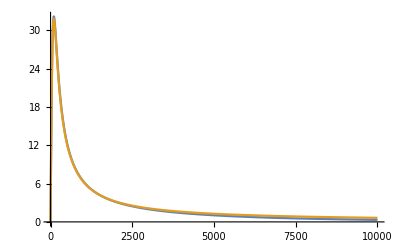

```mathematica
Plot[{J[ω, alpha],Jod[ω, alpha]}, {ω,0, 10000},PlotRange->All]
```

```mathematica
Integrand[ω_, alpha_, β_, t_] := J[ω,alpha]/ω^2 Coth[(ω β)/2] (1-Cos[ω t])
(*Integrand[0, alpha, β, 1]*)
(*Plot[Re@Integrand[ω, alpha, β, 0.1] , {ω, 0.0, 100}, PlotRange->All]*)
```

```mathematica
(*S1:= -4 NIntegrate[J[ω]/ω^2 Coth[ω/(2 kB Temp)], {ω, 0, 10wc}, Method -> {Automatic, "SymbolicProcessing"-> None},MaxRecursion->30 ]*)
S[t_]:=- NIntegrate[J[ω,alpha]/ω^2 Coth[(ω β)/2] (1-Cos[ω t]), {ω, 0.00001, 20000}, Method -> {Automatic, "SymbolicProcessing"-> None},MaxRecursion->100,AccuracyGoal->10]
```

```mathematica
∞
```

∞

```mathematica
Limit[Jod[ω,a]/ω^2 Coth[(ω b)/2] (1-Cos[ω t]), ω->0]
```

(a t^2)/(100 b)

```mathematica
S[1.]
```

-412.947

```mathematica
rho10[t_] := ρ10i Exp[S[t]] Exp[ⅈ ϵ t]
 rho01[t_] := ρ01i Exp[S[t]] Exp[-ⅈ ϵ t]
```

```mathematica
rho10[0.001]
```

-0.203046+0.443663 ⅈ

```mathematica
t0 = 0; tf= 0.02; di =(tf-t0)/2000;
tlist = N[Range[t0,tf, di]];
```

```mathematica
reRho01 =  Re@rho01[tlist];
imRho01 = Im@rho01[tlist];
(*reData = Transpose@{tlist, reRho01};*)
(*imData = Transpose@{tlist, imRho01};*)
(*ListPlot[reData, PlotRange->All]*)
(*ListPlot[Transpose@{tlist, imRho01}, PlotRange->All]*)
```

```mathematica
Directory[]
```

/home/henry

```mathematica
Export["Work/phd-work/vibronic-TLS/DATA/RealExactdata.dat",reData]
Export["Work/phd-work/vibronic-TLS/DATA/ImagExactdata.dat",imData]
```

Work/phd-work/vibronic-TLS/DATA/RealExactdata.dat

Work/phd-work/vibronic-TLS/DATA/ImagExactdata.dat

Absorption Spectra

```mathematica
(*ω0 = 100; Γ=10000;*)
```

```mathematica
μ = 1;
(*α=100; β =10;*)
```

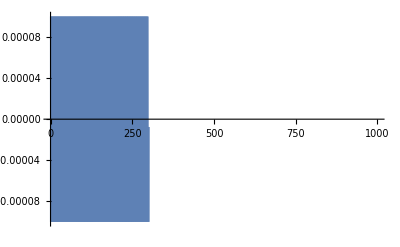

```mathematica
Plot[Re[Jod[ω, alpha]/ω^2 (Cos[ω]Coth[(β ω)/2]+ⅈ Sin[ω])],  {ω,0,300}, PlotRange->{{0, 1000}, {-0.0001, 0.0001}}]
```

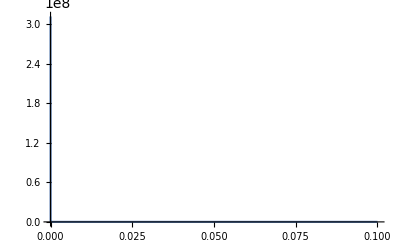

```mathematica
Plot[Jod[ω, alpha]/ω^2, {ω,0,0.1}, PlotRange->All]
```

```mathematica
Assuming[Ω>0&&τ∈Reals,Integrate[(a ω Exp[-ω/Ω])/ω^2 (1-Cos[ω τ]+ⅈ Sin[ω τ]),{ω,0, ∞}]]
```

1/2 a (2 ⅈ ArcTan[τ Ω]+Log[1+τ^2 Ω^2])

```mathematica
(*Φ[τ_] := NIntegrate[(ω Exp[-ω/10])/ω^2 (Cos[ω τ]Coth[(β ω)/2]-ⅈ Sin[ω τ]),{ω,0, ∞} ,Method -> {Automatic, "SymbolicProcessing"-> None},MaxRecursion->40]*)
```

```mathematica
Φ[τ_] := NIntegrate[Jod[ω, alpha]/ω^2 ((1-Cos[ω τ])Coth[(β ω)/2]+ⅈ Sin[ω τ]),{ω,0, ∞} ,Method -> {Automatic, "SymbolicProcessing"-> None},MaxRecursion->40]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

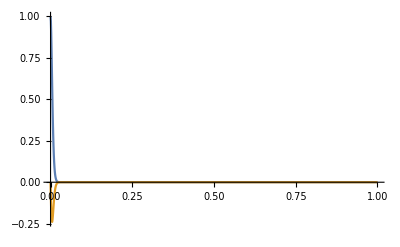

```mathematica
DiscretePlot[{Re[Exp[-Φ[t]]],Im[Exp[-Φ[t]]]},{t,0,1,0.001},PlotRange->All,Joined->True,Filling->None]
```

```mathematica
phi=Interpolation[ParallelTable[{τ,Φ[τ]},{τ,0,0.2,0.0001}]]
```

InterpolatingFunction[{{0., 0.2}}, <>]

```mathematica
Series[Sin[ω τ], {ω, 0, 3}]
```

τ ω-(τ^3 ω^3)/6+O[ω]^4

```mathematica
DiscretePlot[{Re[Exp[-Φ[t]]],Im[Exp[-Φ[t]]]},{t,0,0.2,0.001},PlotRange->All,Joined->True,Filling->None]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

$Aborted

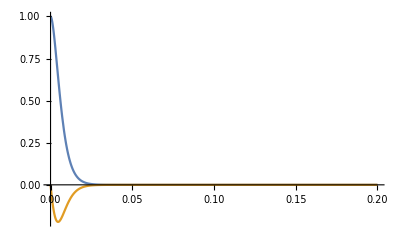

```mathematica
Plot[{Re[Exp[-phi[t]]],Im[Exp[-phi[t]]]},{t,0,0.2},PlotRange->All]
```

```mathematica
shift=NIntegrate[J[ω, alpha]/ω,{ω,0,∞}]
```

100.

```mathematica
S[x_]:=NIntegrate[Exp[-phi[τ] ]Exp[ⅈ(x+shift) τ],{τ, 0, ∞},Method -> {Automatic, "SymbolicProcessing"-> None},MaxRecursion->40]
```

```mathematica
(*S[ω_, ϵ_]:=NIntegrate[Exp[-Φ[τ] ]Exp[ⅈ(ω-ϵ) τ],{τ, 0, ∞},Method -> {Automatic, "SymbolicProcessing"-> None},MaxRecursion->40]*)
```

```mathematica
(*S[ω_, ϵ_]:=NIntegrate[Exp[Φ[τ]-1 ]Exp[i (ω-ϵ) τ],{τ, 0, ∞},Method -> {Automatic, "SymbolicProcessing"-> None},MaxRecursion->40]*)
```

```mathematica
DiscretePlot[Re[S[x]],{x,-1000,1000,10},PlotRange->All,Joined->True,Filling->None]
```

NIntegrate::inumri: The integrand ⅇ^((0.-900. ⅈ) τ-«1») has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{17545.1,1218.17}}.

NIntegrate::inumri: The integrand ⅇ^((0.-890. ⅈ) τ-«1») has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{17545.1,1218.17}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

-Graphics-